Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

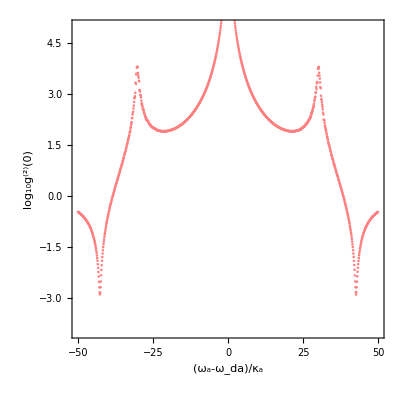

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[200];



data=ParallelTable[
ωr=5.69*2*Pi;
ωge=5.69*2*Pi;


g=0.0135*2*Pi;
γeg=0.0000763*2*Pi;
κ=0.01*2*Pi;
F=0.015*κ;


max1=50*κ;
min1=-50*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=1000;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));
ωgedeviation=10^-5*ωge;
deltadatage=RandomReal[NormalDistribution[ωge,ωgedeviation],Na]-ωge;
gdelta=RandomReal[{0.9*0.0135*2*Pi,1.1*0.0135*2*Pi},Na];
equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*gdelta[[i]]-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+deltadatage[[i]]*ToExpression[StringJoin["Ce1",ToString[i]]]==0,gdelta[[i]]*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]+deltadatage[[i]]*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Pink},Frame->True,PlotRange->{{-50,50},{-4,5}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/J-Cdeltag&deltaz0.015circuit-0.1g.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/J-Cdeltag&deltaz0.015circuit-0.1g.txt",datalist,"Table"];
```

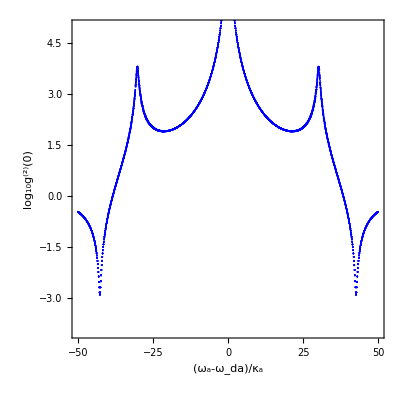

```mathematica
datalist=Import["/home/u000011703749/J-Cdeltag&deltaz0.015circuit-0.1g.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue},Frame->True,PlotRange->{{-50,50},{-4,5}},AspectRatio->1]
```

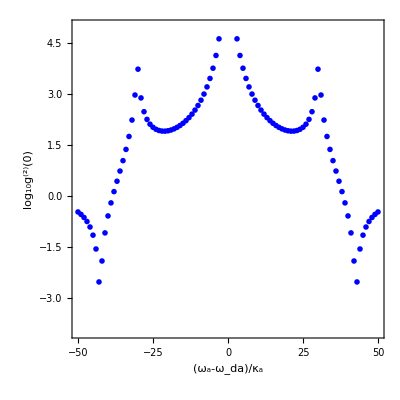
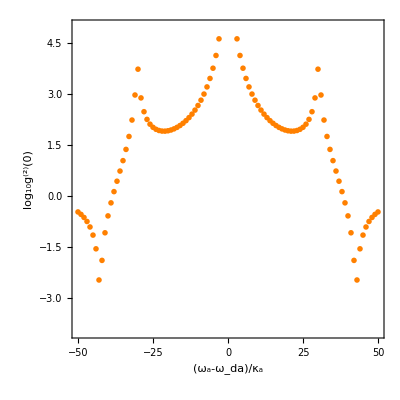
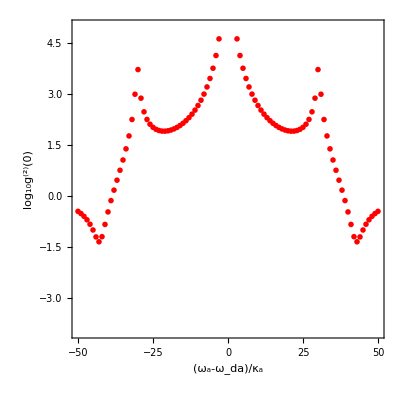
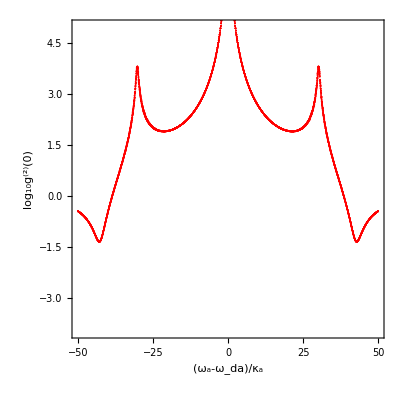
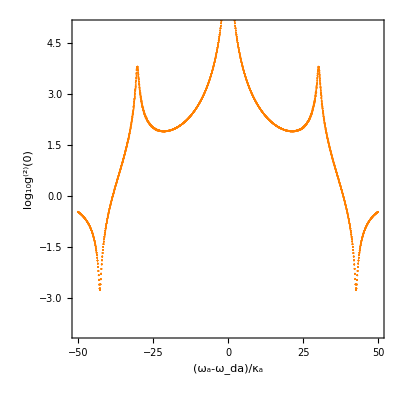
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

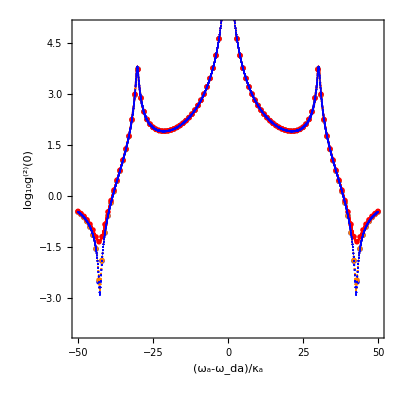

```mathematica
Export["/home/u000011703749/figs2a.pdf",-Graphics-]
```

/home/u000011703749/figs2a.pdf

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

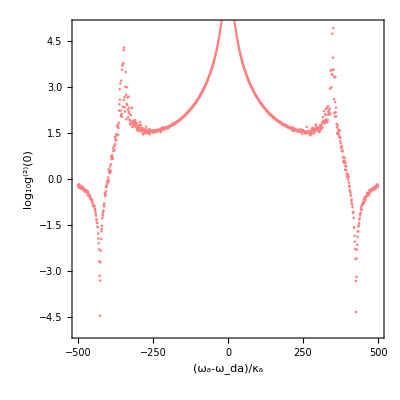

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[200];



data=ParallelTable[
ωr=5.69*2*Pi;
ωge=5.69*2*Pi;


g=10*0.0135*2*Pi;
γeg=0.0000763*2*Pi;
κ=0.01*2*Pi;
F=0.015*κ;


max1=500*κ;
min1=-500*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=1000;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));
ωgedeviation=10^-5*ωge;
deltadatage=RandomReal[NormalDistribution[ωge,ωgedeviation],Na]-ωge;
gdelta=RandomReal[{0,20*0.0135*2*Pi},Na];
equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*gdelta[[i]]-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+deltadatage[[i]]*ToExpression[StringJoin["Ce1",ToString[i]]]==0,gdelta[[i]]*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]+deltadatage[[i]]*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+(Sum[gdelta[[i]]*√2*ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Pink},Frame->True,PlotRange->{{-500,500},{-5,5}},AspectRatio->1]
```

```mathematica
datalist=Import["/home/u000011703749/J-Cdeltag&deltaz0.015circuit-10g.txt","Table"];
datalist=Join[datalist,data];
Export["/home/u000011703749/J-Cdeltag&deltaz0.015circuit-10g.txt",datalist,"Table"];
```

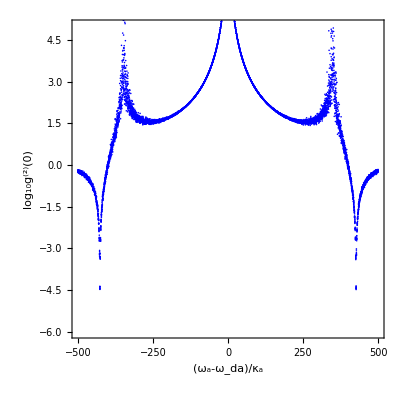

```mathematica
datalist=Import["/home/u000011703749/J-Cdeltag&deltaz0.015circuit-10g.txt","Table"];
ListPlot[datalist,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue},Frame->True,PlotRange->{{-500,500},{-6,5}},AspectRatio->1]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

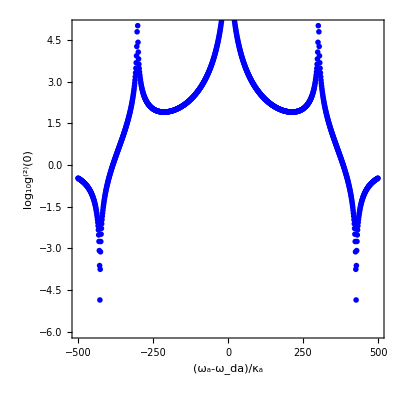

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[200];



data=ParallelTable[
ωr=5.69*2*Pi;
ωge=5.69*2*Pi;


g=10*0.0135*2*Pi;
γeg=0.0000763*2*Pi;
κ=0.01*2*Pi;

F=0.015*κ;
max1=500*κ;
min1=-500*κ;      (*max and min value of Δ*)
segment1=1000;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=1000;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,1000+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->20,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue},Frame->True,PlotMarkers->"OpenMarkers",PlotRange->{{-500,500},{-6,5}},AspectRatio->1]
```

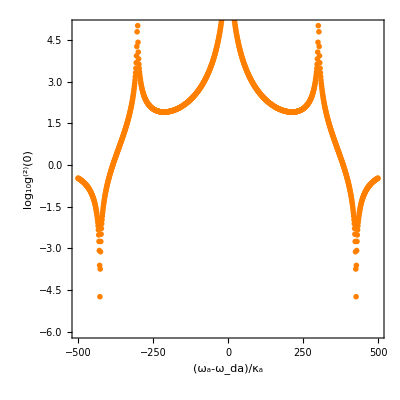
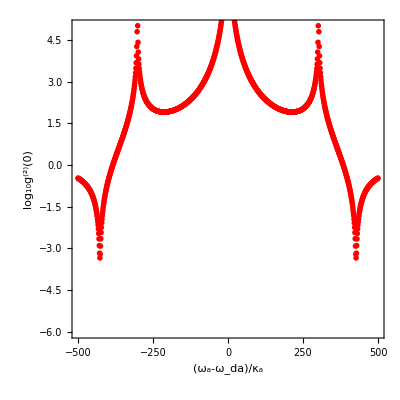
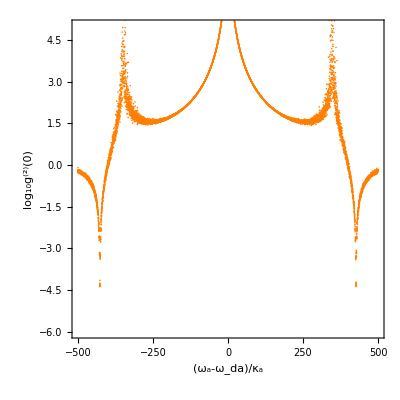
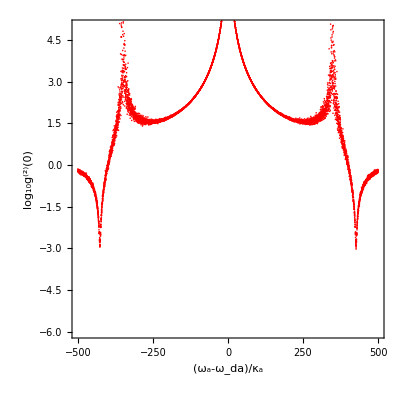
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

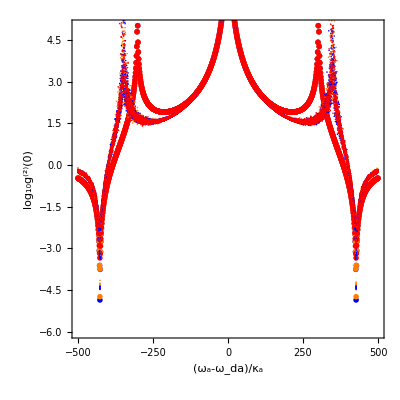

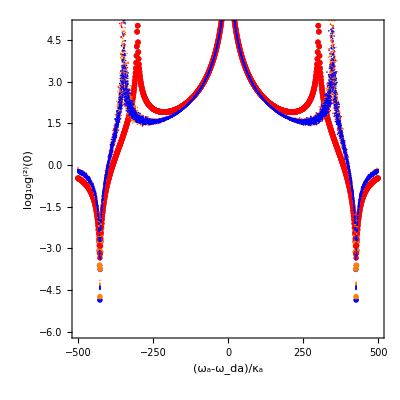

```mathematica
Export["/home/u000011703749/figs2b.pdf",-Graphics-]
```

/home/u000011703749/figs2b.pdf